## Resonances of a forced nonlinear oscillator

Start with a idea the response is known and then calculate stimulus .

```mathematica
x[t_]:= A Sin [ν t] + ϵ B Sin[3 ν t] + ϵ^2 C Sin[5 ν t]
```

```mathematica
duff = x''[t] + ω^2 x + ϵ (α x^3+ 2 γ x'[t]) == 𝒮 Sin[ν t+δ]
```

x ω^2+ϵ (x^3 α+2 γ (A ν Cos[t ν]+3 B ϵ ν Cos[3 t ν]+5 C ϵ^2 ν Cos[5 t ν]))-A ν^2 Sin[t ν]-9 B ϵ ν^2 Sin[3 t ν]-25 C ϵ^2 ν^2 Sin[5 t ν]==𝒮 Sin[δ+t ν]

```mathematica
B = A^3 α / (4 (ω^2 - 9 ν^2))
```

(A^3 α)/(4 (-9 ν^2+ω^2))

```mathematica
ϵ = 1;
```

Solution to a A is:

```mathematica
Clear[A]
```

```mathematica
eq1 =A ==S/(√(((ω^2-ν^2)+3/4 A^2 α )^2+(2 γ ν)^2))
```

A==S/(√(4 γ^2 ν^2+((3 A^2 α)/4-ν^2+ω^2)^2))

```mathematica
Clear[a,v,S,γ,α,ω];
```

```mathematica
eq2 = S^2-((ω^2-v)^2+4 γ^2 v)a-3/2 α(ω^2-v)a^2-9/4 α^2 a^3==0;
```

```mathematica
eq2
```

S^2-(9 a^3 α^2)/4-3/2 a^2 α (-v+ω^2)-a (4 v γ^2+(-v+ω^2)^2)==0

```mathematica
eq2 /.{S->19,ω->1,γ->0., α->4/3}
```

361-4 a^3-a (0.+(1-v)^2)-2 a^2 (1-v)==0

```mathematica
eq2
```

S^2-(9 a^3 α^2)/4-3/2 a^2 α (-v+ω^2)-a (4 v γ^2+(-v+ω^2)^2)==0

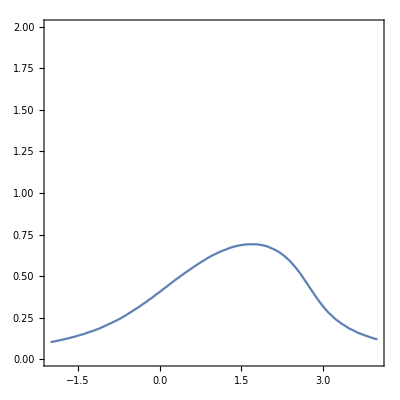

```mathematica
ContourPlot[1-4 a^3-2 a^2 (1-v)-a ((1-v)^2+0)==0, {v,-2,4},{a,0,2}]
```